```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=Flatten[Import["./k1.dat"]];
kappa=Flatten[Import["./y13.dat"]];
Zphi=Flatten[Import["./y10.dat"]];
etaphi=Flatten[Import["./etaphi.dat"]];
(*fpi=Flatten[Import["./fpi.dat"]];
T=Flatten[Import["./TMeV.dat"]];
ListPlot[Transpose[{T,fpi}](*,ScalingFunctions->{"Log",Automatic}*),PlotRange->All]*)
```

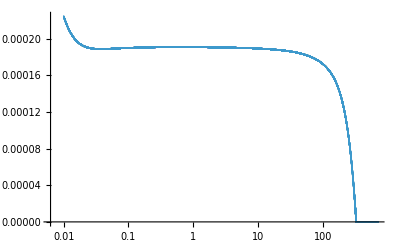

```mathematica
ListPlot[Transpose[{k,kappa/k}],ScalingFunctions->{"Log",Automatic}]
```

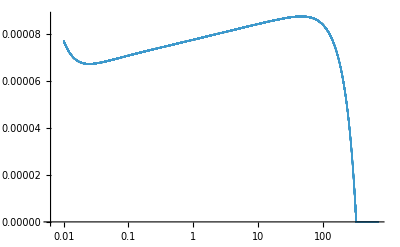

```mathematica
ListPlot[Transpose[{k,kappa/(Zphi k)}],ScalingFunctions->{"Log",Automatic}]
```